Задача 12

Намиране на минимум и максимум на функцията
f[x_] := уравнение;
Print[“Първата производна на функцията f относно x e f’x = “, ∂_x f[x]]
Print[“Втората производна на функцията f относно x  е f’’x = ”, ∂_(x,x) f[x]]
Plot[f[x], {x, -3, 3}, AxesOrigin->{0, 0}]
***графика и принтване***
Solve[∂_x f[x]==0]
**птинтва**
Plot[f’[x], {x, -5, 5}, AxesOrigin->{0, 0}]
**графика**
x1:=корен едно;
x2:=корен две;
f2=f’’;
Print[“За x= ”, x1, “ втората производна е y’’ = ”, f2[x1]]
If[f2[x1]≠0, If[f2[x1]<0, Print[“Функцията има локален максимум в точка x= ”, x1, “, y= ”, f[x1]],
 Print[“Функцията има локален минимум в точка x = ”, x1, “, y = ”, f[x1]]],
 Print[“При x=0 втората производна е равна на 0 и е възможно да е инфлексна точка, трябва да проверим третата производна - ако тя е ненулева, то това е инфлексна точка.”]]
 Print[“За x = ”, x2, “ втората производна е y’’ = ”, f2[x2]]
 If[f2[x2]≠0, If[f2[x2]<0, Print[“Функцията има локален максимум в точка х = ”, x2, “, y = ”, f[x2]],
 Print[“Функцията има локален минимум в точка x = ”, x2, “, y = ”, f[x2]]],
 Print[“При х=0 втората производна е равна на 0 и е възможно да е инфлексна точка, трябва да проверим третата производна - ако тя е ненулева, то това е инфлексна точка. ”]]
 c=Solve[f’[x]==0, x] /*корени на уравнението*/
 points=Points[{x, f[x]}/.c[[{1, 2}]]]
 **принт**
 Plot[f[x], {x, -2, 2.4}, Epilog->{Red, PointSize[.02], points}] /*точки мин и макс*/
 Print[“Функцията е растяща при: ”, Reduce[f’[x]>0, x]]
 Print[“Функцията е намаляваща при: ”, Reduce[f’[x]<0, x]]

Първата производна на функцията f относно x e f'x = -(2 x^2)/((1+x^2)^2)+1/(1+x^2)

Втората производна на функцията f относно x  е f''x = (8 x^3)/((1+x^2)^3)-(6 x)/((1+x^2)^2)

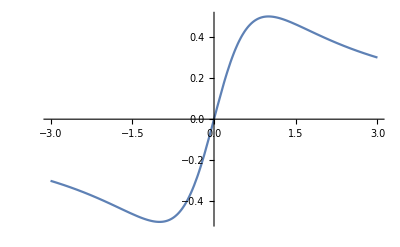

```mathematica
f[x_] := x/(1+x^2);
Print["Първата производна на функцията f относно x e f'x = ", D[f[x], x]]
Print["Втората производна на функцията f относно x  е f''x = ", D[f[x], x,x]]
Plot[f[x], {x, -3, 3}, AxesOrigin->{0, 0}]
```

```mathematica
Solve[D[f[x], x]==0]
```

{{x→-1},{x→1}}

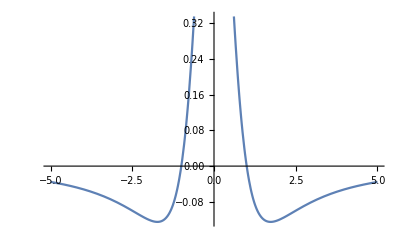

```mathematica
Plot[f'[x], {x, -5, 5}, AxesOrigin->{0, 0}]
```

```mathematica
x1=-1;
```

```mathematica
x2=1;
```

```mathematica
f2=f'';
```

```mathematica
Print["За x= ", x1, " втората производна е y'' = ", f2[x1]]
If[f2[x1]≠0, If[f2[x1]<0, Print["Функцията има локален максимум в точка x= ", x1, ", y= ", f[x1]],
 Print["Функцията има локален минимум в точка x = ", x1, ", y = ", f[x1]]],
Print["При x=0 втората производна е равна на 0 и е възможно да е инфлексна точка, трябва да проверим третата производна - ако тя е ненулева, то това е инфлексна точка."]]
 Print["За x = ", x2, " втората производна е y'' = ", f2[x2]]
If[f2[x2]≠0, If[f2[x2]<0, Print["Функцията има локален максимум в точка х = ", x2, ", y = ", f[x2]],
 Print["Функцията има локален минимум в точка x = ", x2, ", y = ", f[x2]]],
Print["При х=0 втората производна е равна на 0 и е възможно да е инфлексна точка, трябва да проверим третата производна - ако тя е ненулева, то това е инфлексна точка. "]]
```

За x= -1 втората производна е y'' = 1/2

Функцията има локален минимум в точка x = -1, y = -1/2

За x = 1 втората производна е y'' = -1/2

Функцията има локален максимум в точка х = 1, y = 1/2

```mathematica
c=Solve[f'[x]==0,x]
points=Point[{x,f[x]}/.c[[{1,2}]]]
```

{{x→-1},{x→1}}

Point[{{-1,-1/2},{1,1/2}}]

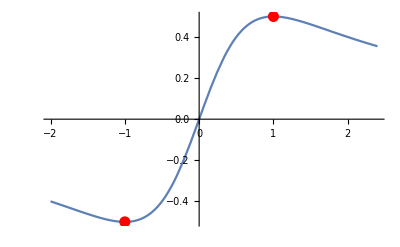

```mathematica
Plot[f[x], {x, -2, 2.4}, Epilog->{Red, PointSize[.02], points}]
```

```mathematica
Print["Функцията е растяща при: ", Reduce[f'[x]>0, x]]
Print["Функцията е намаляваща при: ", Reduce[f'[x]<0, x]]
```

Функцията е растяща при: -1<x<1

Функцията е намаляваща при: x<-1||x>1